```mathematica
A={{1,1/2},{1/2,1}};(*線形変換を表す行列*)
```

```mathematica
A//MatrixForm
```

(1 | 1/2
1/2 | 1)

```mathematica
Det[A]
```

3/4

```mathematica
G[σ_,x_,y_]=Exp[-(x^2+y^2)/(2*σ^2)]/(2Pi*σ)(*ガウスカーネル*)
```

(ⅇ^((-x^2-y^2)/(2 σ^2)))/(2 π σ)

```mathematica
Plot3D[G[1,x,y],{x,-3,3},{y,-3,3},AxesLabel->Automatic,PlotRange->Full]
```

-Graphics3D-

```mathematica
G2[σ_,x_,y_]=Apply[G,Flatten[{σ,Inverse[A].{x,y}}]](*変形したガウスカーネル*)
```

(ⅇ^((-((4 x)/3-(2 y)/3)^2-(-(2 x)/3+(4 y)/3)^2)/(2 σ^2)))/(2 π σ)

```mathematica
Plot3D[G2[1,x,y],{x,-3,3},{y,-3,3},PlotRange->Full,AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
f[x_,y_]=(x-Floor[x])*((y-Floor[y]))(*平滑化対象の関数*)
```

(x-Floor[x]) (y-Floor[y])

```mathematica
Plot3D[f[x,y],{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
f2[x_,y_]=Apply[f,Inverse[A].{x,y}](*変形した平滑化対象の関数*)
```

((4 x)/3-(2 y)/3-Floor[(4 x)/3-(2 y)/3]) (-(2 x)/3+(4 y)/3-Floor[-(2 x)/3+(4 y)/3])

```mathematica
Plot3D[f2[x,y],{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
J1=ParallelTable[NIntegrate[G[1,x-u,y-v]*f[u,v],{u,-Infinity,Infinity},{v,-Infinity,Infinity}],{x,0,2,0.2},{y,0,2,0.2}];(*平滑化*)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in u near {u,v} = {2.,-0.084526}. NIntegrate obtained 0.24999 and 0.0000230476 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in u near {u,v} = {2.,-0.084526}. NIntegrate obtained 0.249996 and 0.000033644 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in u near {u,v} = {-1.99998,-0.084526}. NIntegrate obtained 0.250001 and 0.0000143874 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in u near {u,v} = {2.,-0.084526}. NIntegrate obtained 0.25 and 0.0000148995 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in u near {u,v} = {1.99998,-0.084526}. NIntegrate obtained 0.249987 and 0.0000361606 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 20 recursive bisections in u near {u,v} = {2.,-0.084526}. NIntegrate obtained 0.249998 and 0.0000188688 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in v near {u,v} = {-0.084526,1.99998}. NIntegrate obtained 0.249997 and 0.0000193038 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in u near {u,v} = {1.99998,-0.084526}. NIntegrate obtained 0.249936 and 0.0000227092 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in u near {u,v} = {1.99998,-0.084526}. NIntegrate obtained 0.249983 and 0.0000347235 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in u near {u,v} = {1.99998,-0.084526}. NIntegrate obtained 0.249998 and 0.000048901 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in v near {u,v} = {-0.084526,2.}. NIntegrate obtained 0.25 and 0.000014911 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in u near {u,v} = {2.,-0.084526}. NIntegrate obtained 0.250001 and 0.0000128034 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in u near {u,v} = {1.99998,-0.084526}. NIntegrate obtained 0.249989 and 0.0000670609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in u near {u,v} = {2.,-0.084526}. NIntegrate obtained 0.249997 and 0.0000373345 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in u near {u,v} = {1.99998,-0.084526}. NIntegrate obtained 0.249993 and 0.0000585239 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in u near {u,v} = {2.,-0.084526}. NIntegrate obtained 0.249983 and 0.0000422996 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in u near {u,v} = {1.99998,-0.084526}. NIntegrate obtained 0.24999 and 0.0000678893 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in u near {u,v} = {2.,-0.084526}. NIntegrate obtained 0.249997 and 0.0000441134 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in u near {u,v} = {2.,-0.084526}. NIntegrate obtained 0.250001 and 0.0000454101 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in u near {u,v} = {1.99998,-1.0811}. NIntegrate obtained 0.249988 and 0.0000251442 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in u near {u,v} = {1.99998,0.084526}. NIntegrate obtained 0.249996 and 0.0000324981 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in u near {u,v} = {1.99998,-0.084526}. NIntegrate obtained 0.249985 and 0.000071775 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in u near {u,v} = {1.99998,1.0811}. NIntegrate obtained 0.249994 and 0.0000210938 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in u near {u,v} = {1.99998,0.084526}. NIntegrate obtained 0.249993 and 0.000033524 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
J1//MatrixForm
```

(0.250001 | 0.249997 | 0.25 | 0.249935 | 0.249656 | 0.250002 | 0.250001 | 0.250002 | 0.25 | 0.249997 | 0.250001
0.249997 | 0.25 | 0.25 | 0.25 | 0.250004 | 0.249808 | 0.250001 | 0.249999 | 0.24975 | 0.250001 | 0.249752
0.25 | 0.249936 | 0.250001 | 0.25 | 0.249909 | 0.25 | 0.249896 | 0.249884 | 0.249882 | 0.25 | 0.250001
0.250023 | 0.249969 | 0.249964 | 0.24996 | 0.24996 | 0.249953 | 0.249949 | 0.249946 | 0.249943 | 0.249943 | 0.24994
0.24999 | 0.249987 | 0.249983 | 0.249982 | 0.24998 | 0.249979 | 0.249976 | 0.249976 | 0.249975 | 0.24997 | 0.249973
0.249996 | 0.249991 | 0.249991 | 0.249991 | 0.249992 | 0.24999 | 0.24999 | 0.24999 | 0.249989 | 0.249988 | 0.249988
0.249996 | 0.249998 | 0.249998 | 0.249995 | 0.249996 | 0.249995 | 0.249996 | 0.249995 | 0.249995 | 0.249997 | 0.249994
0.249989 | 0.249997 | 0.249993 | 0.249997 | 0.25 | 0.25 | 0.249999 | 0.249995 | 0.249998 | 0.249997 | 0.249999
0.249983 | 0.24999 | 0.249996 | 0.249997 | 0.249999 | 0.25 | 0.249999 | 0.249999 | 0.249997 | 0.249999 | 0.25
0.249997 | 0.249988 | 0.249994 | 0.249998 | 0.249998 | 0.249999 | 0.250001 | 0.249998 | 0.25 | 0.250002 | 0.249993
0.250001 | 0.249985 | 0.249993 | 0.249996 | 0.249999 | 0.249999 | 0.249999 | 0.250001 | 0.249992 | 0.249999 | 0.250004)

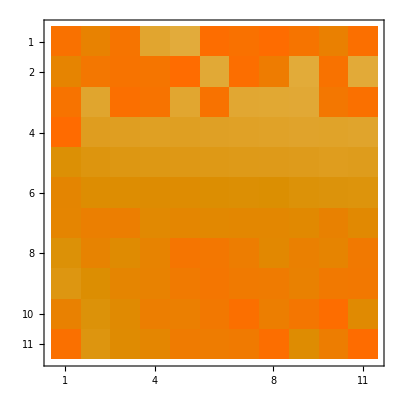

```mathematica
MatrixPlot[J1]
```

```mathematica
J2=ParallelTable[NIntegrate[G2[1,x-u,y-v]*f2[u,v],{u,-Infinity,Infinity},{v,-Infinity,Infinity}],{x,0,2,0.2},{y,0,2,0.2}];(*変形した関数を変形したカーネルで平滑化*)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.187392 and 0.00166036 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.187387 and 0.00160466 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.187391 and 0.0016293 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.187319 and 0.00164928 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.187372 and 0.00164085 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.187342 and 0.00169041 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.187364 and 0.00163801 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.187373 and 0.00160501 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.187391 and 0.0016293 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.187375 and 0.00162713 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.186891 and 0.00157512 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.187417 and 0.0016321 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.187357 and 0.00163546 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.18731 and 0.00161034 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.187349 and 0.00163458 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.187278 and 0.00162704 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.18724 and 0.00162148 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.187248 and 0.00161116 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.187242 and 0.00163675 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.186207 and 0.00150412 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.18728 and 0.00161945 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.187259 and 0.00165229 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.18725 and 0.00165682 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.187331 and 0.00164879 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

```mathematica
J2//MatrixForm
```

(0.187392 | 0.187372 | 0.187391 | 0.187413 | 0.187319 | 0.187333 | 0.187387 | 0.187357 | 0.187278 | 0.18724 | 0.187248
0.187372 | 0.187418 | 0.187364 | 0.187344 | 0.187373 | 0.187323 | 0.187342 | 0.18731 | 0.187242 | 0.186207 | 0.18728
0.187391 | 0.187364 | 0.187375 | 0.187312 | 0.186891 | 0.187424 | 0.187417 | 0.187349 | 0.187259 | 0.18725 | 0.187331
0.187413 | 0.187344 | 0.187312 | 0.18746 | 0.187315 | 0.18734 | 0.187374 | 0.187411 | 0.18738 | 0.187335 | 0.187323
0.187319 | 0.187373 | 0.186891 | 0.187315 | 0.187317 | 0.18727 | 0.187335 | 0.18739 | 0.187365 | 0.187364 | 0.187396
0.187333 | 0.187323 | 0.187424 | 0.18734 | 0.18727 | 0.187322 | 0.187321 | 0.187356 | 0.187339 | 0.187394 | 0.187407
0.187387 | 0.187342 | 0.187417 | 0.187374 | 0.187335 | 0.187321 | 0.187277 | 0.186176 | 0.187345 | 0.187345 | 0.187382
0.187357 | 0.18731 | 0.187349 | 0.187411 | 0.18739 | 0.187356 | 0.186176 | 0.187224 | 0.187328 | 0.187367 | 0.187401
0.187278 | 0.187242 | 0.187259 | 0.18738 | 0.187365 | 0.187339 | 0.187345 | 0.187328 | 0.187363 | 0.187357 | 0.187384
0.18724 | 0.186207 | 0.18725 | 0.187335 | 0.187364 | 0.187394 | 0.187345 | 0.187367 | 0.187357 | 0.187308 | 0.187395
0.187248 | 0.18728 | 0.187331 | 0.187323 | 0.187396 | 0.187407 | 0.187382 | 0.187401 | 0.187384 | 0.187395 | 0.187295)

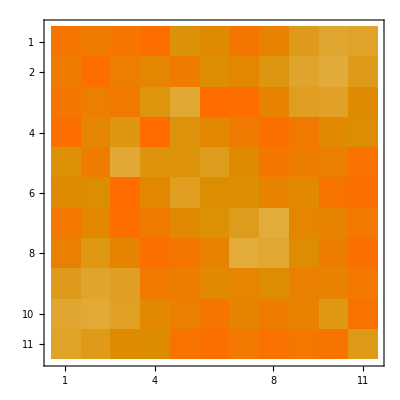

```mathematica
MatrixPlot[J2]
```

```mathematica
J22=Det[Inverse[A]]*J2;
```

```mathematica
J22//MatrixForm
```

(0.249856 | 0.24983 | 0.249855 | 0.249884 | 0.249759 | 0.249778 | 0.24985 | 0.249809 | 0.249704 | 0.249653 | 0.249664
0.24983 | 0.249891 | 0.249819 | 0.249792 | 0.24983 | 0.249764 | 0.249789 | 0.249746 | 0.249656 | 0.248276 | 0.249707
0.249855 | 0.249819 | 0.249833 | 0.24975 | 0.249189 | 0.249899 | 0.24989 | 0.249799 | 0.249679 | 0.249667 | 0.249774
0.249884 | 0.249792 | 0.24975 | 0.249947 | 0.249753 | 0.249787 | 0.249831 | 0.249881 | 0.24984 | 0.24978 | 0.249764
0.249759 | 0.24983 | 0.249189 | 0.249753 | 0.249757 | 0.249693 | 0.24978 | 0.249853 | 0.249821 | 0.249818 | 0.249861
0.249778 | 0.249764 | 0.249899 | 0.249787 | 0.249693 | 0.249763 | 0.249761 | 0.249808 | 0.249785 | 0.249859 | 0.249876
0.24985 | 0.249789 | 0.24989 | 0.249831 | 0.24978 | 0.249761 | 0.249702 | 0.248235 | 0.249793 | 0.249794 | 0.249843
0.249809 | 0.249746 | 0.249799 | 0.249881 | 0.249853 | 0.249808 | 0.248235 | 0.249632 | 0.249771 | 0.249823 | 0.249868
0.249704 | 0.249656 | 0.249679 | 0.24984 | 0.249821 | 0.249785 | 0.249793 | 0.249771 | 0.249817 | 0.249809 | 0.249846
0.249653 | 0.248276 | 0.249667 | 0.24978 | 0.249818 | 0.249859 | 0.249794 | 0.249823 | 0.249809 | 0.249744 | 0.24986
0.249664 | 0.249707 | 0.249774 | 0.249764 | 0.249861 | 0.249876 | 0.249843 | 0.249868 | 0.249846 | 0.24986 | 0.249726)

```mathematica
{0.8,0.8}==Inverse[A].{1.2,1.2}
```

True

```mathematica
J22[[1.2/0.2,1.2/0.2]]
```

0.249763

```mathematica
J1[[0.8/0.2,0.8/0.2]]
```

0.24996